## Smoothing idea

Reference: The natural cubic spline
From: Calculus and Mathematica
Authors :  Bill Davis, Horacio Porta and Jerry Uhl  ©1999

This problem will appeal mainly to enthusiasts.
It is not for everyone.

The natural cubic spline endeavors to put the most artistic curve through a list of points. Here is such a list:

```mathematica
points = {{-8,-12},{-1,-15},{2,20},{5,-4},
           {8,9},{11,3},{15,9}};
```

There are seven points in this list.  One common belief is that the best curve through these points is the unique 6^th degree interpolating polynomial through the points.  Let's plot it.
The equation of this polynomial is:

```mathematica
Clear[x,fitter];
y=Expand[InterpolatingPolynomial[points,x]]
```

86999543/6442254+(612132523 x)/33611760-(1637822117 x^2)/171793440+(136446911 x^3)/154614096+(8114303 x^4)/77307048-(577061 x^5)/32211270+(974513 x^6)/1546140960

And the plot:

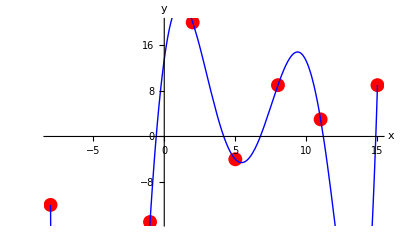

```mathematica
givenpoints=ListPlot[points,PlotStyle->{Red,PointSize[0.025]}];

polythrough=Plot[y,{x,-8,15},PlotStyle->{Blue}];

Show[givenpoints,polythrough,
	AxesLabel->{"x","y"},AspectRatio->1/GoldenRatio]
```

Get real!
Look at that huge dip on the left! 
That polynomial curve has dips and crests that are not suggested by the given points.  You'd better give up on using this approach for this list of numbers.
A drastic measure would be to connect the consecutive points with line segments.  Some folks call this procedure "linear interpolation."  Try it:

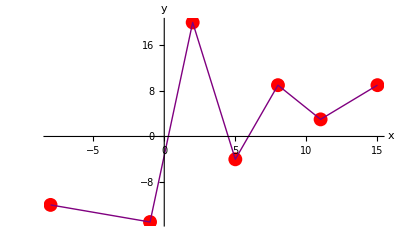

```mathematica
sticks=ListPlot[points,Joined->True,PlotStyle->{Purple}];

Show[givenpoints,sticks,
	AxesLabel->{"x","y"},AspectRatio->1/GoldenRatio]
```

Yuk!  
This is rough, but it is more satisfactory than the polynomial plot.  There must be a way of getting some smoothness into the curve.
Enter the natural cubic spline.

"Freedom is for everyone, but using it wisely 
is the burden of the educated person."
                                                                                               ---------Old Argentine proverb

Instead of passing a line segment through consecutive points, you pass a different cubic curve through each pair of consecutive points, and make a smooth spline with knots at each of the points.
This may seem outlandish at first, because a cubic curve 
     y = a x^3 + b x^2 + c x + d
has four coefficients to determine, and normally you fit a cubic through four points.  But with the cubic spline, you fit the cubic through just two consecutive points and use the extra freedom you have to guarantee smoothness at the knots on the left and right of the knot.
Start out with the points above
     {x[1],y[1]}, {x[2],y[2]}, {x[3],y[3]}, 
     {x[4],y[4]}, {x[5],y[5]}, {x[6],y[6]}, and
     {x[7],y[7]},
sorted so that the x[k]'s increase as k increases.

```mathematica
Clear[x,y,K];
points = N[Sort[points]];
x[k_]:= points[[k,1]];
y[k_]:= points[[k,2]];
K = Length[points]
```

7

f[k,x] is the cubic that you are going to run from
     {x[k], y[k]} to {x[k+1], y[k +1]}:

```mathematica
Clear[f,a,b,c,d,k,eqn];
f[k_,x_]=a[k] x^3+b[k] x^2+c[k] x+d[k]
```

x^3 a[k]+x^2 b[k]+x c[k]+d[k]

Here k runs from k = 1 to k = 6 (= K-1); so you are working with 6 cubics, f[1,x], f[2,x], ... , f[6,x], and each cubic has 4 undetermined (so far) coefficients.  This means you've got 24 equations to play with.
To hit the points, you want:
     f[k,x[k]] = y[k] for k = 1, 2, 3, 4, 5, 6,

```mathematica
eqns1=Table[f[k,x[k]]==y[k],{k,1,K-1}]
```

{f[1,-8.]==-12.,f[2,-1.]==-15.,f[3,2.]==20.,f[4,5.]==-4.,f[5,8.]==9.,f[6,11.]==3.}

and
     f[k,x[k+1]] = y[k+1] for k = 1, 2, 3, 4, 5, 6.

```mathematica
eqns2=Table[f[k,x[k+1]]==y[k+1],{k,1,K-1}]
```

{f[1,-1.]==-15.,f[2,2.]==20.,f[3,5.]==-4.,f[4,8.]==9.,f[5,11.]==3.,f[6,15.]==9.}

For smoothness at the knots, you want:
     f'[k,x[k]] = f'[k-1,x[k]] for k = 2, 3, 4, 5, 6,
 and
      f''[k,x[k]] = f''[k-1,x[k]] for k = 2, 3, 4, 5, 6.
Here, all derivatives are with respect to the x variable.

```mathematica
eqns3 = Table[(D[f[k,x],x] == D[f[k-1,x],x])/.x->x[k],
				  {k,2,K-1}]
```

{f^(0,1)[2,-1.]==f^(0,1)[1,-1.],f^(0,1)[3,2.]==f^(0,1)[2,2.],f^(0,1)[4,5.]==f^(0,1)[3,5.],f^(0,1)[5,8.]==f^(0,1)[4,8.],f^(0,1)[6,11.]==f^(0,1)[5,11.]}

```mathematica
eqns4 = Table[(D[f[k,x],{x,2}] == D[f[k-1,x],{x,2}])/.x->x[k],
				  {k,2,K-1}]
```

{f^(0,2)[2,-1.]==f^(0,2)[1,-1.],f^(0,2)[3,2.]==f^(0,2)[2,2.],f^(0,2)[4,5.]==f^(0,2)[3,5.],f^(0,2)[5,8.]==f^(0,2)[4,8.],f^(0,2)[6,11.]==f^(0,2)[5,11.]}

You cannot use k = 1 in the last two equations because there is no function f[0, x].
So far you have specified
     6 + 6 + 5 + 5 = 22 
conditions, and you have 24 undetermined coefficients; as a result you need to specify two more conditions.
Old-timers at the art of curve fitting have found that good results usually come from specifying that the second derivatives equal 0 at the endpoints, {x[1], y[1]} and {x[7], y[7]}.  They call the resulting spline "the natural cubic spline."

```mathematica
eqns5 = {(D[f[1,x],{x,2}]/.x->x[1]) == 0,
		       (D[f[K-1,x],{x,2}]/.x->x[K]) == 0}
```

{f^(0,2)[1,-8.]==0,f^(0,2)[6,15.]==0}

Now put all of these equations together.

```mathematica
equations=Join[eqns1,eqns2,eqns3,eqns4,eqns5];
```

Solve for the correct coefficients (all 24 of them), substitute, and plot:

```mathematica
coefflist=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
coeffs=Chop[Solve[equations,coefflist][[1]] ]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Now stick all of these coefficients into the formulas for the f[k,x]'s and define the natural cubic spline function.

```mathematica
Clear[spline,t,k,g];
g[k_,t_]:=f[k,t]/.coeffs;

Do[With[{m=k,n=k+1},spline[t_]:=g[m,t]/;x[m]≤t<x[n]],{k,K-1}]
```

Plot it and see what what happened.

```mathematica
splineplot=Plot[spline[t],{t,x[1],x[K]},
		AspectRatio->1/GoldenRatio,PlotStyle->{Thickness[0.01],Red},PlotRange->All,AxesLabel->{"x","y"}]
```

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

Throw in the points:

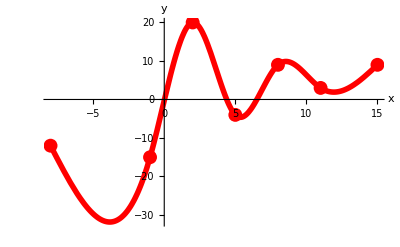

```mathematica
Show[splineplot,givenpoints]
```

There it is!
Golly, that's just about the way most folks would have connected the dots with a pencil.  The old-time cubic spliners seem to know what they're talking about.  
To add adventure to an already thrilling subject, show both the interpolating polynomial and the natural spline on the same plot:

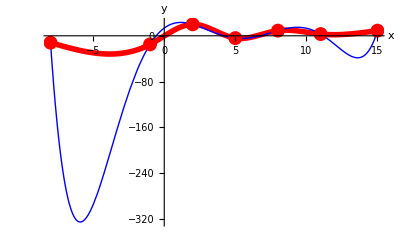

```mathematica
Show[splineplot,polythrough,givenpoints,
	PlotRange->All,AxesLabel->{"x","y"},DisplayFunction->$DisplayFunction]
```

The natural cubic spline shines.
Sit back and reflect, remembering that you are one of an elite group of calculus students who have ever seen a cubic spline.

#### G.6.a.i)

How does the natural cubic spline compare to Mathematica's built in Interpolation function?

#### Answer furnished to you as a gesture of good will:

Try it and see:

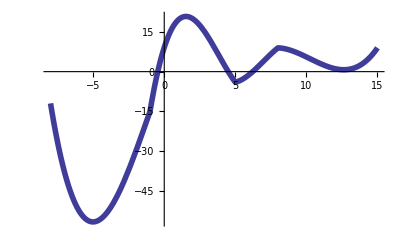

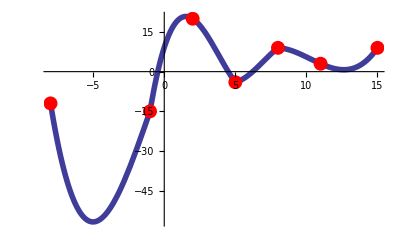

```mathematica
MathematicaDefault=Plot[Interpolation[points][x],{x,-8,15},
		PlotStyle->{{Thickness[0.01]}}]

Show[MathematicaDefault,givenpoints]
```

Uh-oh; hints of rough corners. 
The Mathematica Interpolation function is not a smooth spline. Here are the natural cubic spline and the Mathematica default Interpolation function shown together:

```mathematica
Show[MathematicaDefault,splineplot,givenpoints,DisplayFunction->$DisplayFunction]
```

-Graphics-

The cubic spline emerges as the winner.

#### G.6.a.ii)

Does this mean that everyone ought to give up on Mathematica's Interpolation function and use the natural cubic spline instead?

Answer furnished to you as another gesture of good will:

No. You have to go to a lot of trouble to get the natural cubic spline.  You can get the Mathematica Interpolation function by typing only one line.  Besides, for most situations, the default Mathematica interpolating function is good enough.  But when you want something artistic, the natural cubic spline may be the way to go.

### How can you use this in 3D?

I have not carried the idea below out, but give this a try

Given a bunch of 3D points (x_i,y_i,z_i).
Think of them as aparameterized functions (x(t),y(t),z(t)) with 
x(i)=x_i
y(i)=y_i
z(i)=z_i

Now apply the natural cubic spline to each of the functions above.
This will result into 3 spines
(spine_x(t), spine_y(t), spine_z(t))
Plotted as ParametricPlot3D this will go through all the points (x_i,y_i,z_i).

You may have to play with this a bit to get it to close.